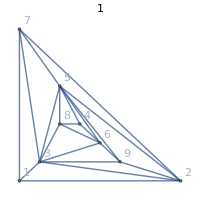
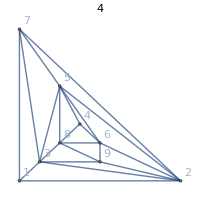
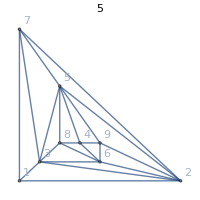
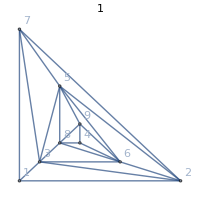
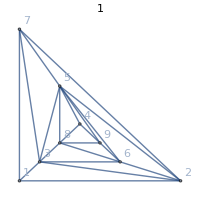
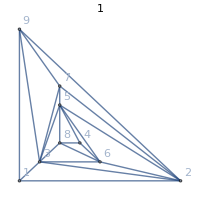
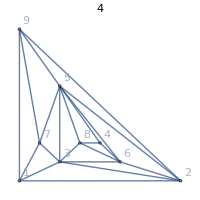
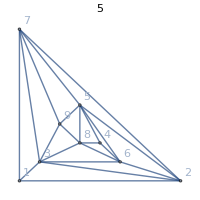

```mathematica
Map[Graph[#,GraphLayout->"PlanarEmbedding", VertexLabels->"Name", ImageSize->200, PlotLabel->ChromaticPolynomial[#,4]/24]&,Select[Table[ReadGrof[k],{k,Range[500]}],Length[VertexList[#]]==9&]]
```